# Numerical Diagonalisation of an arbitrary* Hamiltonian

## TODO

• evolve in time (to prove eigenstate)
• compare diag speed to wick rotation

## Initialisation

```mathematica
ClearAll["Global`*"]
```

```mathematica
AutoCollapse[] := 
  If[$FrontEnd =!= $Failed, 
   SelectionMove[EvaluationNotebook[], All, GeneratedCell];
   FrontEndTokenExecute["SelectionCloseUnselectedCells"]]
```

```mathematica
normaliseDiscrete[psi_, grid_] :=
	psi / √((grid[[2]] - grid[[1]])Total[Abs[psi]^2])
```

```mathematica
(*
plotDiscreteSpectrum[{eigvals_, eigfuncs_}, grid_, range_:All, potential_:(0 &), potentialScaling_:1] :=
	Legended[
		Manipulate[
			Overlay[{
				Show[
					plotDiscreteψ[
						eigfuncs[[n]], 
						grid,
						range
					],
					ListLinePlot[ 
						MapThread[({#1, #2/potentialScaling}&), {grid, potential}],
						Filling->Axis,
						PlotStyle->{Thick, Red}
					]
				],
				Text["E = " <> ToString[eigvals[[n]]]]
			}],
			{n, 1, Length[eigvals], 1},
			SaveDefinitions->True
		],
		colorBar[Arg[ϕ]]
	]
*)
```

```mathematica
(*
presentSpectrum[{x_, xL_, xR_, Δx_}, V_, range_:All, numModes_:10, vScaling_:1] :=
	Module[
		{grid, potential, eigfuncs, eigvals},
			
		grid = Range[xL, xR, Δx];
		potential = If[
			V === 0,
			ConstantArray[0, Length[grid]],
			(V /. x -> #1 &) @ grid
		];
		
		(* add very high potential to end-points to improve stability; finite differences :'c  *)
		potential[[1]] = potential[[-1]] = 10^4;
		
		{eigvals, eigfuncs} = getEigenmodes[potential, grid, numModes];
		plotDiscreteSpectrum[{eigvals, eigfuncs}, grid, range, potential, vScaling]
]
*)
```

## Numerical diagonalisation

```mathematica
getLaplacianMatrix[gridsize_] :=
	SparseArray[
		{
			{i_,i_} :> -5/2,  (* https://mathematica.stackexchange.com/questions/114953/fast-eigensystem-calculation *)
			{i_,j_} :> 4/3   /; Abs[i-j] == 1,
			{i_,j_} :> -1/12 /; Abs[i-j] == 2
		},
		{gridsize, gridsize}
	]
	
getPotentialMatrix[potential_, gridsize_] :=
	SparseArray[{i_, i_} :> potential[[i]], {gridsize, gridsize}]
	
getHamiltonianMatrix[potential_, gridsize_, gridspace_] :=
	getPotentialMatrix[potential, gridsize] - 1/2 getLaplacianMatrix[gridsize] / gridspace^2
	
getEigenmodes::usage = "getEigenmodes[discreteV, grid, numModes] returns numModes many {eigvals, eigmodes}";
	
getEigenmodes[potential_, grid_, numModes_:10] :=
	Module[
		{H, V, ϕ, λ},
		
		(* let's repair potential here too, just to be safe *)
		V = potential;
		V[[1]] = V[[-1]] = 10^4;
		
		H = getHamiltonianMatrix[V, Length[grid], grid[[2]] - grid[[1]]];
		{λ, ϕ} = N[Eigensystem[H, -numModes]];
		{λ, ϕ} = {λ[[#]], ϕ[[#]]}& @ Ordering[λ];
		{λ, ϕ} = {λ, normaliseDiscrete[#, grid]& /@ ϕ}
	]
```

## Testing on a harmonic potential

Consider V = 1/2 x^2

```mathematica
presentSpectrum[{x, -5, 5, 0.05}, x^2/2, {0, 0.6}, 10, 10] // Timing
```

Show::gcomb: Could not combine the graphics objects in Show[plotDiscreteψ[{-2.93451×10^-8,-1.3305×10^-6,-2.80153×10^-6,-4.44078×10^-6,-6.33138×10^-6,«41»,-0.0196205,-0.0224283,-0.0255739,-0.0290879,«151»},{-5.,«49»,«151»},{0,0.6}],].

N[] in matrix: E_10=9.53698  in 0.16s

no change without N[]

## Testing on an infinite potential well

Why is this so expensive? Boundary acts like an infinite potential well!

```mathematica
presentSpectrum[
	{x, -1, 1, 0.01}, 
	0, 
	{-0.3, 2}, 
	10, 
	1
]
```

Adding very high potential either side before the boundary seems to improve numerics (speed and accuracy)

## Testing on other junk

```mathematica
presentSpectrum[
	{x, -5, 5, 0.01}, 
	9999 UnitStep[-(x+2)] + 10 UnitStep[x-2] - 10 UnitStep[x-3], 
	{-0.3, 2}, 
	10, 
	10
]
```

Show::gcomb: Could not combine the graphics objects in Show[plotDiscreteψ[{8.6189×10^-18,-2.02701×10^-17,-1.1669×10^-17,-3.34751×10^-17,-1.3164×10^-17,«41»,2.66792×10^-17,3.08878×10^-17,-8.78749×10^-18,1.2393×10^-17,«951»},{«1»},{-0.3,2}],].

n = 10 is an interesting state of above, where a maximum appears within a region of greater potential. This may be the threshold where this becomes more energetically favourable than “cramming” more lobes into the region of lesser potential, analogous to oscillator modes of higher energy. That is; gradients (through the Laplacian) are energetic in the Schrodinger equation!

```mathematica
presentSpectrum[{x, -5, 5, 0.01}, 10 Exp[-x^2] + x^4/2, {0, 1}, 10, 10]
```

Show::gcomb: Could not combine the graphics objects in Show[plotDiscreteψ[{-4.01864×10^-18,6.21432×10^-18,5.9243×10^-18,7.07898×10^-18,-7.85504×10^-18,«41»,-1.87426×10^-13,-2.30126×10^-13,-2.82299×10^-13,-3.46003×10^-13,«951»},{«1»},{0,1}],].

```mathematica
presentSpectrum[
	{x, -5, 5, 0.01}, 
	6 Exp[-x^2] + 4 Exp[-(x-1)^2] - 5 Exp[-(x+1)^2] - 7 Exp[-10^2(x-2)^4] + x^4/2, 
	{-0.3, 2}, 
	10, 
	10
]
```

Show::gcomb: Could not combine the graphics objects in ….

Accuracy can be tested by propagating these functions through time to observe static profile

## Testing Accuracy

Remember that the smaller the energy eigenvalue, the slower the eigenfunction’s phase will evolve in time!

```mathematica
solveEvolution::usage = "returns an interpolator of the spacetime evolution of a continuous wavefunction";

solveEvolution[psi_, potential_, {xL_, xR_}, duration_:1] :=
	NDSolveValue[
		{
			ⅈ Derivative[0,1][ψ][x, t] ==  -Derivative[2,0][ψ][x, t] / 2 + ψ[x, t] potential[x],
			ψ[x, 0] == psi[x],
			ψ[xL, t] == 0,
			ψ[xR, t] == 0
		},
		ψ, 
		{x, xL, xR},
		{t, 0, duration}
	];

solveDiscreteEvolution::usage = "returns an interpolator of the spacetime evolution a discrete wavefunction";
				
solveDiscreteEvolution[ϕlist_, Vlist_, grid_, duration_:1] :=
	Module[
		{xL, xR, psi, ϕclone, potential, evol},
		xL = grid[[1]];
		xR = grid[[-1]];
		
		(* enforce boundary conditions *)
		ϕclone = ϕlist;
		
		(*
		ϕclone[[1]] = ϕclone[[-1]] = 0;
		*)
	
			
		(* build continuous functions for evolution *)
		psi = ListInterpolation[ϕclone, {{xL, xR}}, Method -> "Spline"];
		potential = ListInterpolation[Vlist, {{xL, xR}}, Method -> "Spline"]; 
		solveEvolution[psi, potential, {xL, xR}, duration]
	]
	
animateDiscreteEvolution::usage = "returns an animation of the spacetime evolution of a discrete wavefunction";
		
animateDiscreteEvolution[ϕlist_, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{evol},
		evol = solveDiscreteEvolution[ϕlist, Vlist, {grid[[1]], grid[[-1]]}, duration];
		Animate[
			plotContinuousψ[evol[x, t], {x, grid[[1]], grid[[-1]]}, False],
			{t, 0, duration}
		]
	]
	
animateEigensystemEvolutionNEW[{eigvals_, eigfuncs_}, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{solutions},
		solutions[n_] := 
			solutions[n] = solveDiscreteEvolution[eigfuncs[[n]], Vlist, grid, duration];
		Manipulate[
			plotContinuousψ[solutions[n][x, t], {x, grid[[1]], grid[[-1]]}, False],
			{t, 0, duration},
			{n, 1, Length[eigfuncs], 1},
			ContinuousAction -> False
		]
	]
	
animateEigensystemEvolution[{eigvals_, eigfuncs_}, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{animFunc},
		animFunc[n_] := 
			animFunc[n] = animateDiscreteEvolution[eigfuncs[[n]], Vlist, grid, duration];
		Manipulate[
			animFunc[n],
			{n, 1, Length[eigfuncs], 1},
			ContinuousAction -> False
		]
	]
```

```mathematica
animateSpectrum[{x_, xL_, xR_, Δx_}, V_, numModes_:4, duration_:1] :=
	DynamicModule[
		{grid, potential, eigfuncs, eigvals},
			
		grid = Range[xL, xR, Δx];
		potential = If[
			V === 0,
			ConstantArray[0, Length[grid]],
			(V /. x -> #1 &) @ grid
		];
		
		(* add very high potential to end-points to improve stability; finite differences :'c  *)
		potential[[1]] = potential[[-1]] = 10^4;
		
		{eigvals, eigfuncs} = getEigenmodes[potential, grid, numModes];
		animateEigensystemEvolutionNEW[{eigvals, eigfuncs}, potential, grid, duration]
]
```

# plotFunctions package test

```mathematica
Get[NotebookDirectory[] <> "plotFunctions.m"]
```

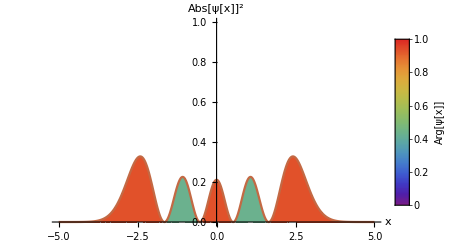

```mathematica
plotWavefunction[daeq[#,0.1]&, {-5, 5}]
```

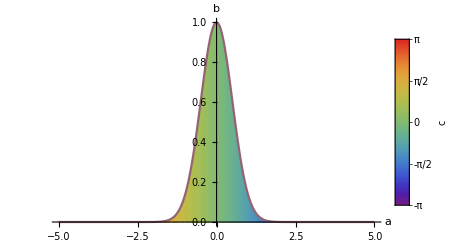

```mathematica
plotWavefunction[
	Exp[-x^2] Exp[- ⅈ x ], {x, -5, 5},
	plotRange -> {0, 1},
	showBar -> True,
	labels -> {a, b, c}
]
```

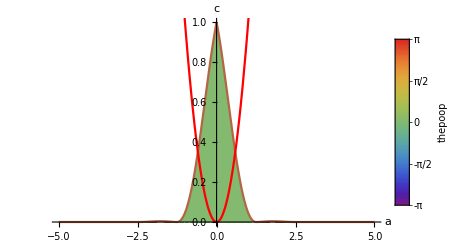

```mathematica
plotWavefunction[{0, 0, 0, 0, 1, 0, 0, 0, 0}, {-5, 5}, labels -> {a, c, thepoop}]
```

```mathematica
plotWavefunction[x, {x, -5, 5}]
```

plotFunctions`Private`plotContinuousWavefunction[x/.{x,-5,5}⟦1⟧→#1&,{-5,5},ReplaceAll[{(plotFunctions`Private`potential→plotFunctions`Private`symb$_):>plotFunctions`Private`potential→(plotFunctions`Private`symb$/.{x,-5,5}⟦1⟧:>#1&)}]]